```mathematica
Integrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π},Assumptions->{r>0}]
```

$Aborted

```mathematica
FullSimplify[1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ]]
```

Sin[θ]/(4 π (1/8+(-2+w+2 Cos[Cos[ϕ] Sin[θ]])^2))

```mathematica
FullSimplify[(-128Cos[x]+64+64 Cos[x]^2)^(1/2)]
```

8 √((-1+Cos[x])^2)

```mathematica
(((1.913*2.818)^2)*1.0/(2*π*1.0))*2
```

9.25043

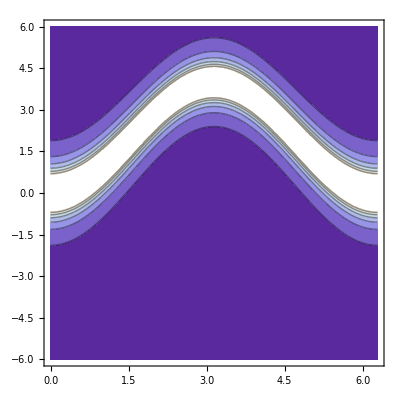

```mathematica
ContourPlot[2*(((1.913*2.818)^2)*1.0/(2*π*1.0))((14.7-(2-2Cos[kx]))/14.7)1/π(1/2(1/2))/((1/2(1/2)^2)+(w-(2-2Cos[kx]))^2),{kx,0,2π},{w,-6,6}]
```

```mathematica
(Exp[(2-2Cos[1])/(8.617343*10^-2*0.0001)]-1)^-1
```

3.665606056×10^-46336

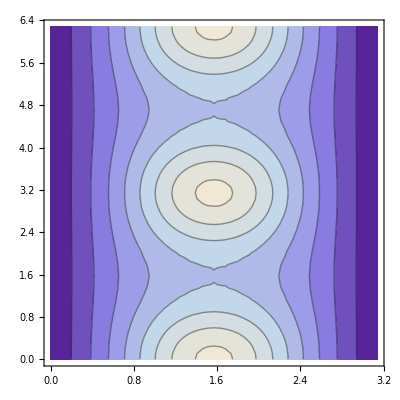

```mathematica
ContourPlot[1/π(1/2(1/2))/((1/2(1/2)^2)+(4-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
NIntegrate[1/π(1/2(1/2))/((1/2(1/2)^2)+(0-(2-2Cos[1Sin[θ]Cos[ϕ]]))^2)Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

5.04313

```mathematica
2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[kx]))/14.7)*
```

9.25043

```mathematica
vals=Table[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[kx]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[kx]))^2),{w,0,5,.2},{kx,0,π,.2}];
```

```mathematica
2*4/π//N
```

2.54648

```mathematica
Max[vals]
```

23.556

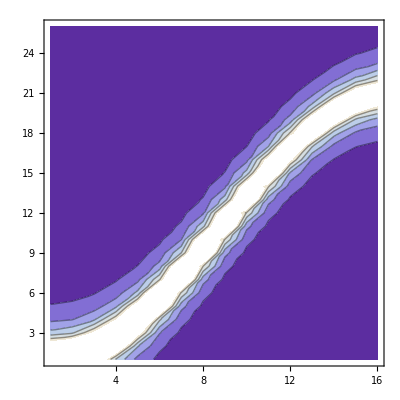

```mathematica
ListContourPlot[vals]
```

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{r,0.1,π,π/30},{w,0,5,1/6}]//Quiet
```

{{2.8775,2.05627,1.07257,0.60034,0.367283,0.247706,0.18017,0.131532,0.101851,0.0792848,0.065267,0.0555003,0.0455383,0.0389817,0.0334439,0.029389,0.0254983,0.0230648,0.0204624,0.0184442,0.0164078,0.0151386,0.0137163,0.0126504,0.0115384,0.0104948,0.0098696,0.0091413,0.00843022,0.00790212,0.00736843},{12.345,9.08323,4.81504,2.65062,1.58273,1.05121,0.745866,0.560773,0.426214,0.344431,0.275728,0.231536,0.190485,0.162964,0.141824,0.125174,0.109083,0.0953604,0.0868085,0.0772818,0.0686842,0.0636276,0.0571937,0.0530703,0.0479308,0.0452688,0.0412535,0.0381525,0.0353174,0.0339275,0.0309856},{27.7807,21.4038,11.4427,6.3688,3.81497,2.5124,1.80748,1.29783,0.991575,0.808948,0.65045,0.537747,0.456501,0.386689,0.325797,0.284898,0.259204,0.224139,0.199092,0.178914,0.162113,0.147696,0.13166,0.123536,0.111595,0.10576,0.0954242,0.0884096,0.0825899,0.0758698,0.0720332},{46.96,41.5895,23.3491,12.3982,7.3722,4.75094,3.31042,2.42993,1.87746,1.49032,1.20476,0.987034,0.80739,0.695503,0.604168,0.523447,0.468428,0.40719,0.357185,0.324358,0.29308,0.27136,0.241118,0.221799,0.200657,0.187937,0.173789,0.15718,0.146761,0.139552,0.126763},{67.4023,67.1607,42.1194,22.4051,12.9536,8.27634,5.67825,4.04626,3.10882,2.46749,1.93282,1.61107,1.34461,1.13736,0.971538,0.846063,0.744609,0.654286,0.581289,0.522045,0.466804,0.428806,0.376511,0.348175,0.328456,0.30383,0.270779,0.256382,0.239915,0.220185,0.207268},{89.321,95.5211,68.3643,39.1817,22.1387,13.5647,9.14407,6.41881,4.85558,3.71463,3.00647,2.42827,2.00784,1.72086,1.45384,1.25978,1.08304,0.976751,0.867505,0.759838,0.692832,0.629082,0.563278,0.513378,0.478201,0.440326,0.404036,0.373164,0.345923,0.314799,0.297702},{108.986,121.618,99.8156,67.5668,37.7046,21.9964,14.1308,9.756,7.2131,5.55377,4.33197,3.48149,2.93224,2.436,2.03643,1.78051,1.55308,1.38004,1.21194,1.08625,0.953431,0.862105,0.791691,0.720033,0.655883,0.621473,0.561376,0.524826,0.483028,0.450388,0.415111},{128.651,143.223,126.805,97.6332,63.5714,36.8152,23.0383,14.8027,10.8077,8.06838,6.16617,5.06056,4.04719,3.40579,2.88029,2.4267,2.14097,1.89304,1.64988,1.46572,1.29756,1.17393,1.07349,0.970371,0.891884,0.822512,0.756017,0.692027,0.640431,0.596067,0.542784},{145.088,168.153,149.598,127.376,98.5744,66.1399,39.0035,23.8522,16.2168,11.6546,8.86955,6.87112,5.66941,4.59708,3.84956,3.33697,2.82424,2.44531,2.18848,1.98111,1.74838,1.53819,1.39313,1.27497,1.17559,1.05452,0.986223,0.897149,0.840917,0.765791,0.719047},{165.108,187.586,166.965,149.323,124.275,99.7545,68.8065,41.9776,25.7738,17.7972,12.7971,9.83528,7.80233,6.38855,5.31152,4.34619,3.80343,3.28725,2.82293,2.55926,2.25628,2.01067,1.80534,1.64682,1.48546,1.32945,1.23571,1.13646,1.05384,0.987544,0.906838},{189.426,208.723,193.28,169.59,147.399,128.335,106.216,73.9363,45.493,27.8221,19.4534,14.296,11.0336,8.55828,7.00507,5.89768,4.86775,4.32283,3.69923,3.28767,2.87389,2.57903,2.31966,2.06974,1.86554,1.7279,1.58004,1.42956,1.30265,1.22801,1.13083},{203.484,230.092,215.255,187.929,167.18,149.983,132.816,112.178,81.5616,49.9679,31.2178,21.2894,15.6141,11.8553,9.56837,7.86698,6.49803,5.51104,4.76418,4.23177,3.65407,3.25849,2.86043,2.64576,2.30612,2.10822,1.96529,1.76998,1.64942,1.5552,1.39023},{220.075,253.815,228.246,204.881,184.013,164.678,151.913,135.868,116.858,90.0321,58.0302,35.7998,24.246,17.3557,13.2506,10.6427,8.80704,7.23237,6.19399,5.31208,4.67283,4.13091,3.61066,3.28576,2.9198,2.60647,2.39287,2.19249,2.00697,1.85756,1.74666},{237.326,270.371,245.723,222.649,203.105,182.724,166.885,156.264,142.625,124.743,101.467,67.3048,41.6312,27.1651,19.5215,14.7708,11.6118,9.81526,8.16485,6.70725,5.91045,5.14192,4.52887,4.0301,3.60119,3.1884,2.9915,2.73318,2.40181,2.2683,2.06417},{258.536,297.345,265.443,234.717,217.701,196.007,182.603,170.538,158.287,144.689,131.266,112.317,80.1732,47.959,31.1105,21.9079,16.4691,13.1733,10.667,9.01145,7.47334,6.42943,5.66068,4.99808,4.47707,4.00285,3.58501,3.25526,2.97016,2.72935,2.42322},{276.915,313.526,284.908,254.881,230.14,212.841,193.906,182.635,171.583,166.605,153.411,139.889,123.122,92.3936,56.6439,36.1052,24.8726,18.4219,14.6792,11.843,9.56862,8.22311,7.19052,6.21472,5.45449,4.8472,4.3083,3.9751,3.56098,3.28038,2.96351},{286.694,337.434,304.819,275.416,243.594,228.011,211.796,198.916,182.666,178.203,170.422,159.502,150.093,131.358,103.249,67.5775,42.1972,28.3735,20.7839,16.4279,12.9771,10.7914,9.13586,7.81391,6.78737,5.92096,5.32229,4.75357,4.33519,3.94753,3.51845},{311.486,351.249,323.944,285.403,263.943,243.376,220.847,213.775,200.114,191.604,185.331,176.313,167.329,156.763,142.868,114.743,80.103,49.0887,32.4411,22.8044,17.9579,14.2751,11.8785,9.73677,8.50283,7.6096,6.49591,5.76463,5.23004,4.70977,4.2924},{334.373,365.149,346.419,306.133,278.4,253.487,240.,225.473,215.739,201.91,195.881,186.104,183.019,173.694,165.767,154.633,132.601,92.4399,55.7215,36.4089,25.8768,19.5003,15.758,12.8375,10.9526,9.33373,8.07266,7.14866,6.27068,5.63382,5.00838},{345.019,391.658,360.804,328.154,291.666,270.58,253.394,237.447,225.68,216.328,205.697,205.112,193.042,192.465,182.46,177.961,165.529,144.565,101.859,62.7124,40.9171,28.8755,21.4341,16.9783,13.7936,11.8768,10.0841,8.73806,7.6486,6.9177,6.05009},{363.805,414.012,383.516,342.056,309.322,284.199,260.012,252.011,238.088,227.538,217.23,211.704,208.002,205.926,201.246,194.65,186.484,177.199,158.835,111.647,70.0917,44.4671,31.1573,23.0885,18.4878,15.1015,12.772,10.7211,9.39958,8.31168,7.27959},{380.929,435.586,396.207,352.92,320.81,301.005,278.297,264.334,246.089,241.904,229.065,223.442,215.927,215.35,216.079,210.995,203.011,200.817,189.17,166.727,122.792,74.7143,46.9597,34.0244,25.1314,19.7975,15.6438,13.5672,11.5391,10.096,8.59844},{395.018,453.647,422.483,382.841,342.535,304.677,286.882,271.447,262.32,251.041,239.786,239.281,237.053,229.907,225.154,223.379,222.014,217.788,213.97,205.308,179.015,127.041,78.8869,49.0124,34.6644,26.2607,20.6533,16.8814,14.1461,12.2699,10.4282},{417.516,473.394,437.27,385.64,357.864,326.247,308.685,284.013,279.271,263.736,254.569,251.937,243.491,239.209,234.952,237.83,235.735,236.131,232.164,235.768,217.433,190.705,130.942,77.8516,50.2341,35.5748,26.8784,21.3742,17.5795,14.7355,12.6945},{433.337,496.987,457.769,402.413,371.992,339.846,320.579,297.279,292.209,271.825,267.307,265.761,256.013,250.208,252.068,249.243,245.849,251.7,254.056,254.756,248.85,237.403,191.769,125.531,74.5197,50.6618,35.8474,27.6406,22.0411,18.0763,15.7135},{457.486,514.164,472.146,423.307,386.302,356.904,330.749,308.898,300.243,279.45,278.593,271.408,267.923,263.815,266.162,262.177,258.173,264.367,269.902,276.237,278.533,274.052,249.414,187.035,111.654,69.9185,47.7475,35.1683,27.0699,21.7149,18.4696},{467.008,538.345,484.842,449.672,393.408,368.906,345.868,325.864,309.11,295.832,291.471,284.706,279.626,274.371,272.259,274.068,271.919,283.187,283.649,288.155,302.766,307.691,308.658,262.074,166.843,98.2578,63.7995,45.3447,33.6942,26.8022,22.2426},{485.045,552.647,512.715,457.316,420.698,385.843,356.593,332.937,324.054,309.349,302.642,297.63,290.884,291.654,283.897,287.019,284.212,289.317,297.815,304.555,324.523,336.672,350.332,323.426,232.71,138.29,84.5433,58.4592,41.3586,32.4808,26.3868},{499.663,568.988,526.457,477.253,438.453,407.733,368.421,347.753,333.409,320.922,322.688,301.325,303.913,293.512,296.062,297.236,303.309,307.75,310.702,326.364,347.813,370.536,391.642,388.632,308.451,184.59,110.68,72.26,51.4357,38.9665,30.8437},{512.787,601.797,546.108,483.772,445.232,409.818,386.914,366.148,343.713,331.507,324.806,318.738,308.184,307.638,315.349,308.779,310.143,323.019,323.614,339.343,359.724,388.192,428.861,455.313,391.228,240.592,139.022,89.5213,61.4898,45.7321,36.5979}}

```mathematica
{523.344637790916,555.9775801528555,450.06826127053,382.71046461343843,347.73005630451695,325.8338326661845,315.42654257661275,308.86972242582453,316.8065973058143,325.9091444272565,367.1680606203278,425.17102547928755,389.53220933181194,138.88782240241227,62.103054915446,36.40288824724365}-{467.069221453134,519.808010478993,292.322299510204,287.244284529843,338.980954219716,379.727324543641,162.435417988404,36.4186853770459,618.010974246558,315.216512739039,312.100549953185,301.621675124277,394.876533038488,434.581085996050,65.3287841142702,0}
```

{56.2754,36.1696,157.746,95.4662,8.7491,-53.8935,152.991,272.451,-301.204,10.6926,55.0675,123.549,-5.34432,-295.693,-3.22573,36.4029}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(0-(2-2Cos[r Sin[θ]Cos[ϕ]]))^2)r^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{r,0,π,π/15}]//Quiet
```

{0.,13.005,48.1068,89.2859,129.107,167.846,202.105,238.385,273.563,307.764,342.279,382.823,418.046,455.433,495.278,517.866}

```mathematica
lst=Table[NIntegrate[2((((1.913*2.818)^2)*1.0/(2*π*1.0)))((14.7-(2-2Cos[π Sin[θ]Cos[ϕ]]))/14.7)*1/π(2*1/2(1/2))/((1/2(1/2))^2+(w-(2-2Cos[π Sin[θ]Cos[ϕ]]))^2)π^2 Sin[θ],{θ,0,π},{ϕ,0,2π},Method->{"MonteCarlo"}],{w,0,5,1/3}]//Quiet
```

{523.345,555.978,450.068,382.71,347.73,325.834,315.427,308.87,316.807,325.909,367.168,425.171,389.532,138.888,62.1031,36.4029}

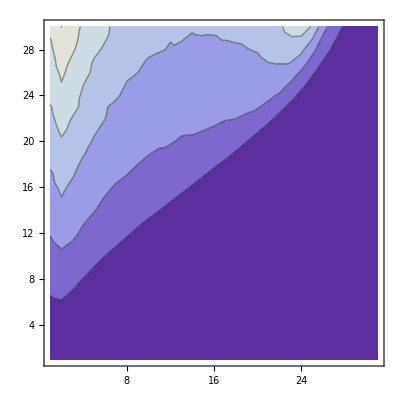

```mathematica
ListContourPlot[lst]
```

```mathematica
((1.913*2.818^2)*1.0/(2*π*1.0))((14.7-(2-2Cos[r Sin[θ]Cos[ϕ]]))/14.7)
```

2.41778